```mathematica
Lx=16;
Ly=16;
Lz =19;
A=Lx*Ly*Lz;
```

```mathematica
Clear[Sitelocation,FlatSite,Sites, LineUp,LineDn]
```

```mathematica
Sitelocation=Table[{i,j},{i,1,Lx},{j,1,Ly}];
```

```mathematica
FlatSite=Flatten[Sitelocation];
```

```mathematica
NOrbitals2D=Dimensions[FlatSite][[1]]
```

512

```mathematica
Sites=Table[{FlatSite[[i]],FlatSite[[i+1]]},{i,1,NOrbitals2D,2}];
```

```mathematica
(**--Equations for the two red lines--**)
```

```mathematica
LineUp[x_]:=(2/3)*(x-1)+6
LineDn[x_]:=(2/3)*(x-2)+4
```

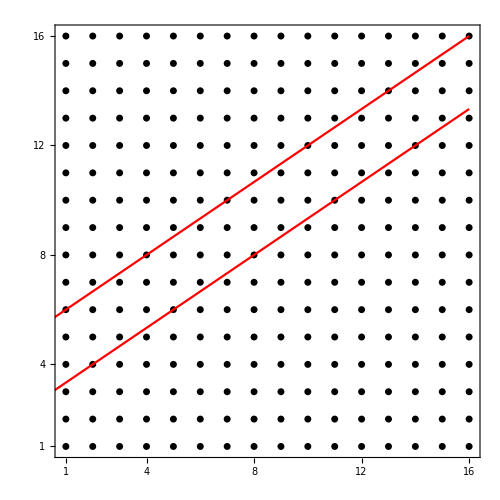

```mathematica
Show[ListPlot[Sites,PlotStyle-> {Black,PointSize[0.01]},Frame-> True,Axes-> False,PlotRange-> {{0.9,Lx+0.1},{0.9,Ly+0.1}}],
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,0,Lx},PlotStyle-> Red],
Plot[LineDn[x],{x,0,Lx},PlotStyle-> Red],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"}},None}},
ImageSize-> 500,AspectRatio-> 1
]
```

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[Fibonup,Fibondown,TotalFibon,XList, YList, XListKron, YListKron, BottIndexQuasi]
```

```mathematica
(**-----We want to count points inside the area of interest, store them in FibonupNew, and sort them into Fibonup-----**)
```

```mathematica
Clear[FibonupNew]
FibonupNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
Do[Do[FibonupNew=Append[FibonupNew,x+(y-1)*Lx],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx}]
```

```mathematica
FibonupNew;
```

```mathematica
Fibonlist2D=Sort[FibonupNew]
```

{49,65,66,67,82,83,84,99,100,101,102,117,118,119,134,135,136,137,152,153,154,169,170,171,172,187,188,189,204,205,206,207,222,223,224,239,240}

```mathematica
Clear[XList,YList,ZList,zzz1,XList2D,YList2D]
```

```mathematica
XList2D =Mod[Fibonlist2D,Lx,1]
```

{1,1,2,3,2,3,4,3,4,5,6,5,6,7,6,7,8,9,8,9,10,9,10,11,12,11,12,13,12,13,14,15,14,15,16,15,16}

```mathematica
YList2D =Ceiling[Fibonlist2D/Lx]
```

{4,5,5,5,6,6,6,7,7,7,7,8,8,8,9,9,9,9,10,10,10,11,11,11,11,12,12,12,13,13,13,13,14,14,14,15,15}

```mathematica
Dimensions[XList2D]
```

{37}

```mathematica
XList = {};
YList={};
ZList = {};
```

```mathematica
Do[XList = Append[XList,XList2D ],{n,1,Lz}]
```

```mathematica
XList = Flatten[XList];
```

```mathematica
Do[YList = Append[YList,YList2D ],{n,1,Lz}]
```

```mathematica
YList = Flatten[YList];
```

```mathematica
zzz1 = Table[1,{n,1,Dimensions[XList2D][[1]]}]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Do[ZList = Append[ZList,zzz1 * m],{m,1,Lz}]
```

```mathematica
ZList = Flatten[ZList];
```

```mathematica
Fibonlist={};
```

```mathematica
Do[Fibonlist = Append[Fibonlist,Fibonlist2D+n*Lx*Ly],{n,0,Lz-1}];
```

```mathematica
Fibonlist;
```

```mathematica
Fibonlist=Sort[Flatten[Fibonlist]];
```

```mathematica
(**----Group the orbitals in the sites in Fibonlist ---**)
```

```mathematica
Fibonup = 2 * Fibonlist -1;
```

```mathematica
Fibondown = 2 * Fibonlist;
```

```mathematica
(**-- Fibondown=Table[Fibonlist[[j]]+A,{j,1,Dimensions[Fibonlist][[1]]}]; --**)
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon = Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

1406

```mathematica
NOrbitalsQuasi/2
```

703

```mathematica
NOrbitalsQuasi2D = NOrbitalsQuasi/Lz
```

74

```mathematica
NOrbitalsOutside = NOrbitals2D*Lz-NOrbitalsQuasi
```

8322

```mathematica
PercentageDataIn = N[NOrbitalsQuasi/(2*A)]
```

0.144531

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{9728}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
Clear[τ,ν,x,Fibon1D,largestX]
```

```mathematica
τ=1/D[LineUp[x],x];
ν=√(1+τ^2);
```

```mathematica
x[m_]:=m/ν+1/(τ*ν)*Round[m/τ]
```

```mathematica
Fibon1D=Table[{1+N[x[m]],0},{m,0,NOrbitalsQuasi2D/2-1}]
```

{{1.,0},{1.9245,0},{2.4792,0},{3.4037,0},{4.3282,0},{4.8829,0},{5.8074,0},{6.7319,0},{7.2866,0},{8.2111,0},{9.1356,0},{9.6903,0},{10.6148,0},{11.5393,0},{12.094,0},{13.0185,0},{13.943,0},{14.4977,0},{15.4222,0},{16.3467,0},{16.9014,0},{17.8259,0},{18.7504,0},{19.3051,0},{20.2296,0},{21.1541,0},{21.7088,0},{22.6333,0},{23.5578,0},{24.1125,0},{25.037,0},{25.9615,0},{26.5162,0},{27.4407,0},{28.3652,0},{28.9199,0},{29.8444,0}}

```mathematica
largestX=Ceiling[Fibon1D[[Dimensions[Fibon1D][[1]],1]]]
```

30

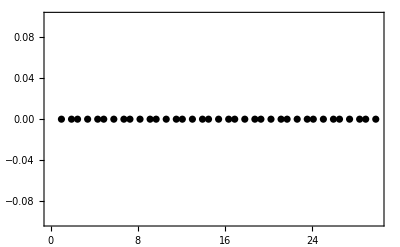

```mathematica
ListPlot[Fibon1D,Frame-> True,Axes-> False,PlotRange->{{0,largestX},{-0.1,0.1}},PlotStyle-> Black,PlotStyle->Small]
```

```mathematica
Fibon1D[[3,1]]
```

2.4792

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[TabFibonacci]
```

```mathematica
J=NOrbitalsQuasi/2;
```

```mathematica
TabFibonacci=Import["/home/archisman/Documents/GitHub/quasicrystals/data-generated-by-prof-bitan/FermiArcReal/LDOSFermiArcReal_161619_Rational_3D_Up+6_Dn+4.dat"];
```

```mathematica
Clear[rng,P1]
```

```mathematica
rngOld={0,Max[#]}&@(TabFibonacci[[All,3]])
```

{0,0.0146963}

```mathematica
rng = {0,0.0148}
```

{0,0.0148}

```mathematica
rng[[2]]
```

0.0148

```mathematica
colorfunc=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
P1=BarLegend[{colorfunc[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.0"},{rng[[2]]/2,"6.5"},{rng[[2]]-0.2*10^-3,"13.0"}}]
```

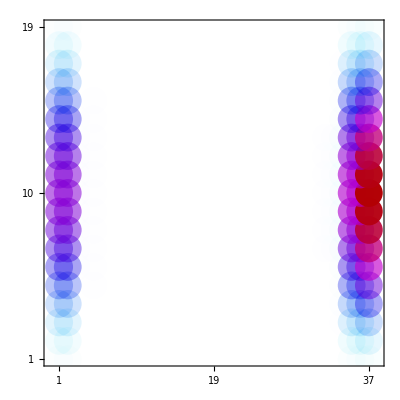

```mathematica
Show[Graphics[{PointSize[0.05],colorfunc[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibonacci,
Frame->True,FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
BaseStyle-> 18,
PlotRange-> {{0,37+1},{1,Lz}}],
(* ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.015]}],*)
FrameTicks->{{{1,Ceiling[Lz/2],Lz},None},{{1,19,37},None}},RotateLabel-> False,
AspectRatio->1
]
```

```mathematica
(** Export["dataFermiArcReal_Rational_3D_Up+6_Dn+4.dat",TabFibonacci]; **)
```